## Symbolic

```mathematica
Clear[dw, lp, β, ds, dj, o]
```

```mathematica
b = {Cos[α], Sin[α]} dw/2
```

{1/2 dw Cos[α],1/2 dw Sin[α]}

```mathematica
αl = α-90°+β
```

-90 °+α+β

```mathematica
l = {Cos[αl], Sin[αl]} (lp-ds/2)
```

{(-ds/2+lp) Sin[α+β],-(-ds/2+lp) Cos[α+β]}

```mathematica
αe = αl-90°
```

-180 °+α+β

```mathematica
e = {Cos[αe], Sin[αe]} (dj+ds)/2
```

{-1/2 (dj+ds) Cos[α+β],-1/2 (dj+ds) Sin[α+β]}

```mathematica
s = {o, h}
```

{o,h}

```mathematica
(b+l+e-s)[[1]]
```

-o+1/2 dw Cos[α]-1/2 (dj+ds) Cos[α+β]+(-ds/2+lp) Sin[α+β]

```mathematica
Solve[(b+l+e-s)[[2]]==0, {h}]
```

{{h→1/2 (ds Cos[α+β]-2 lp Cos[α+β]+dw Sin[α]-dj Sin[α+β]-ds Sin[α+β])}}

### Example

```mathematica
dw = 250;
lp = 139;
β=15°;
ds = 12;
dj = 12;
o = 48;
```

```mathematica
FindRoot[b+l+e-s , {{α, 120°}, {h, dw}}]
```

{α→2.05309,h→191.995}

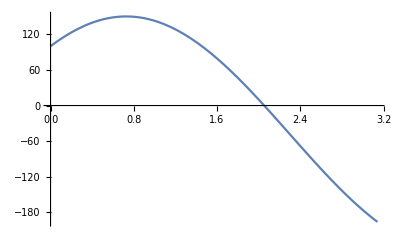

```mathematica
Plot[(b+l+e-s)[[1]], {α, 0, 180°}]
```